Паде - аппроксимация: 1.3.6 [0/n]

Реализация функции:

```mathematica
padeApprox[func_,n_Integer]:= Module[
{taylor = Series[1/func, {x,0,n}], 
approx},
approx = (Normal@taylor)^-1;
Plot[{func, approx},{x,-Pi,Pi},
AspectRatio->Automatic,Filling->Axis,PlotLegends->{func, approx}]
]
```

Результат работы алгоритма :

Пример 1

```mathematica
func = Sin[x];
```

n=1

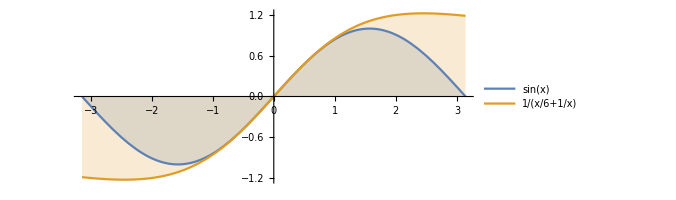

n=6

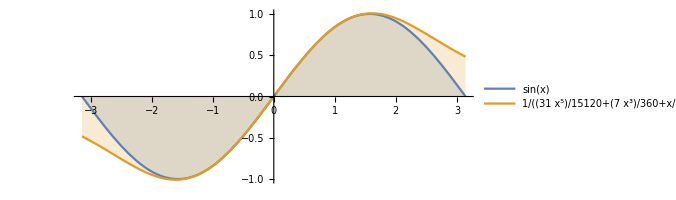

n=11

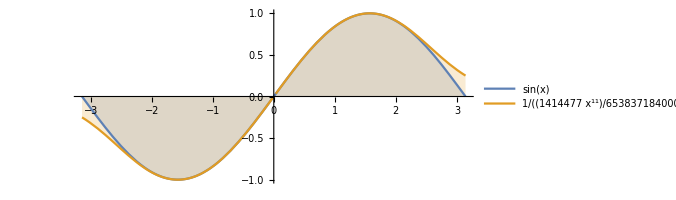

```mathematica
Do[Print["n=",n];Print[padeApprox[Sin[x],n]],{n,1,15,5}]
```

Пример 2

```mathematica
func = Cos[x];
```

n=3

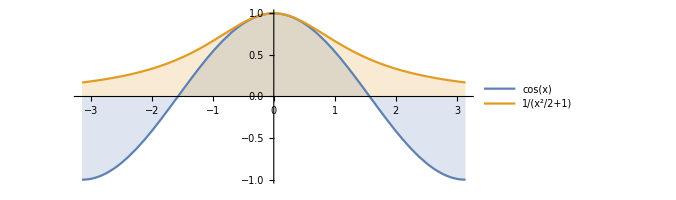

n=8

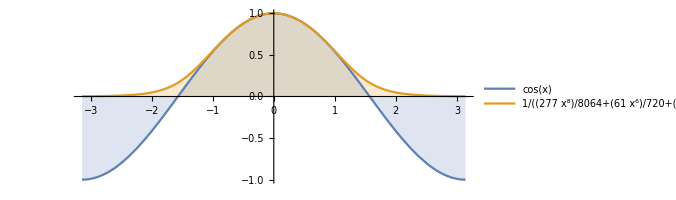

n=13

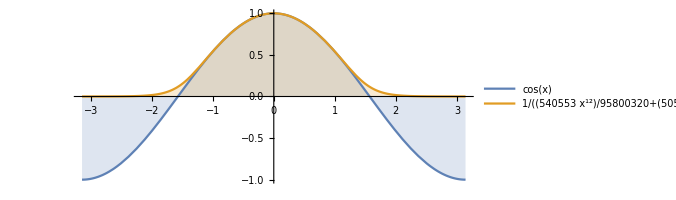

```mathematica
Do[Print["n=",n];Print[padeApprox[Cos[x],n]],{n,3,15,5}]
```

Пример 3

```mathematica
func = ArcTan[x];
```

n=1

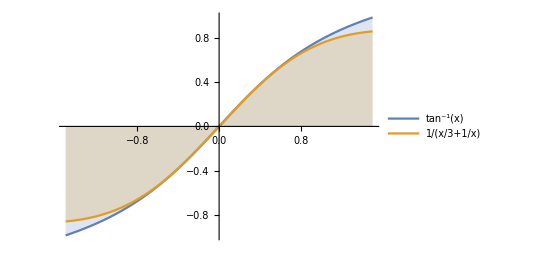

n=4

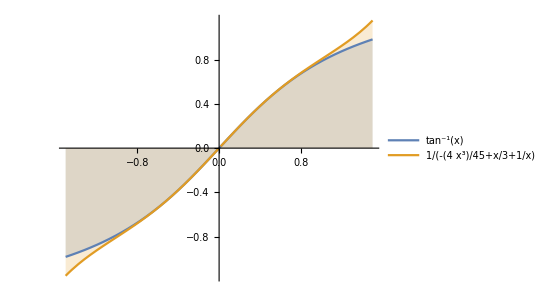

n=7

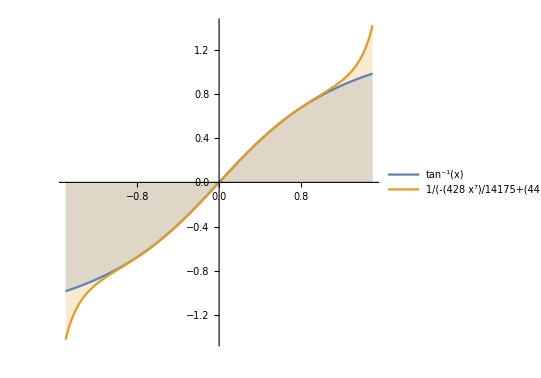

```mathematica
Do[Print["n=",n];Print[padeApprox[ArcTan[x],n]],{n,1,9,3}]
```

Пример 4

```mathematica
func = Log[x];
```

n=1

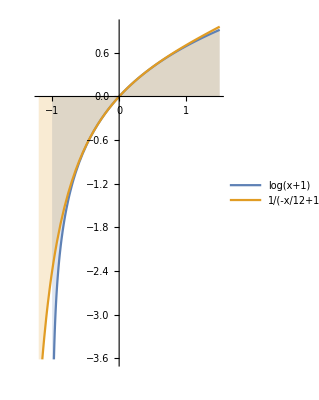

n=3

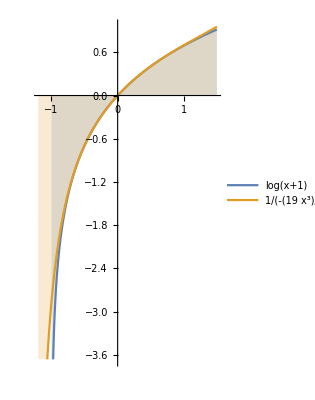

n=5

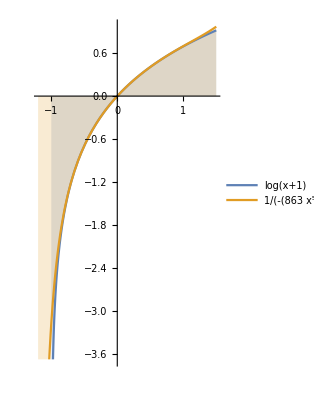

```mathematica
Do[Print["n=",n];Print[padeApprox[Log[x+1],n]],{n,1,5,2}]
```